## 非线性方程求解

```mathematica
ε=10^-9;
f[x_]=2x^4+24x^3+61x^2-16x+1;
linecolor=Array[RGBColor[N[(#/20)^2],N[Sqrt[#/20]],N[E^(-#)],0.5]&,20]
```

{RGBColor[0.0025, 0.22360679774997896, 0.36787944117144233, 0.5],RGBColor[0.01, 0.31622776601683794, 0.1353352832366127, 0.5],RGBColor[0.0225, 0.3872983346207417, 0.049787068367863944, 0.5],RGBColor[0.04, 0.4472135954999579, 0.01831563888873418, 0.5],RGBColor[0.0625, 0.5, 0.006737946999085467, 0.5],RGBColor[0.09, 0.5477225575051661, 0.0024787521766663585, 0.5],RGBColor[0.1225, 0.5916079783099616, 0.0009118819655545162, 0.5],RGBColor[0.16, 0.6324555320336759, 0.00033546262790251185, 0.5],RGBColor[0.2025, 0.6708203932499369, 0.00012340980408667956, 0.5],RGBColor[0.25, 0.7071067811865475, 0.000045399929762484854, 0.5],RGBColor[0.3025, 0.7416198487095663, 0.00001670170079024566, 0.5],RGBColor[0.36, 0.7745966692414834, 6.14421235332821*^-6, 0.5],RGBColor[0.4225, 0.806225774829855, 2.2603294069810542*^-6, 0.5],RGBColor[0.49, 0.8366600265340756, 8.315287191035679*^-7, 0.5],RGBColor[0.5625, 0.8660254037844386, 3.059023205018258*^-7, 0.5],RGBColor[0.64, 0.8944271909999159, 1.1253517471925912*^-7, 0.5],RGBColor[0.7225, 0.9219544457292888, 4.139937718785167*^-8, 0.5],RGBColor[0.81, 0.9486832980505138, 1.522997974471263*^-8, 0.5],RGBColor[0.9025, 0.9746794344808963, 5.602796437537268*^-9, 0.5],RGBColor[1., 1., 2.061153622438558*^-9, 0.5]}

## Newton法

```mathematica
f'[x]
φ[x_]=x-f[x]/f'[x]
```

-16+122 x+72 x^2+8 x^3

x-(1-16 x+61 x^2+24 x^3+2 x^4)/(-16+122 x+72 x^2+8 x^3)

初值为0

```mathematica
Subscript[x, 0] = 0;
X=N[NestWhileList[φ,Subscript[x, 0],Abs[f[#]]>=ε&]]
Length[X]-1
Show[Plot[Callout[f[x],"f(x)",{0.05,0.7},0.03,Background->None,Appearance->"CurvedLeader",LabelStyle->Directive[Italic]],{x,-0.05,0.15},PlotStyle->Directive[RGBColor[0.9,0.5,0.5],Thick],PlotRange->{-0.5,1.5},AxesLabel->{x,y},LabelStyle->Directive[FontFamily->"Century Schoolbook"]],Plot[Evaluate[Table[f'[t](x-t)+f[t],{t,X}]],{x,-0.05,0.15},PlotRange->{-0.5,1.5},PlotStyle->linecolor],ListPlot[Table[Callout[{X[[k]],0},Subscript["x", k-1],Below,LabelStyle->Directive[Italic,FontFamily->"Century Schoolbook"]],{k,1,5}]],
Graphics[{Dashed,Table[Line[{{X[[k]],0},{X[[k]],f[X[[k]]]}}],{k,1,3}]}]]
```

{0.,0.0625,0.0926751,0.107509,0.114853,0.118484,0.120243,0.121026,0.121284,0.12132,0.12132}

10

-Graphics-

#### 迭代阶估计

(1.2132034356×10^-1
5.882034356×10^-2
2.8645198737×10^-2
1.381118333×10^-2
6.4671097966×10^-3
2.8366620379×10^-3
1.0777367851×10^-3
2.9452566089×10^-4
3.6510853775×10^-5
7.1688628629×10^-7
2.8745411607×10^-10)

(-2.1093207643
-2.833267505
-3.5527694332
-4.2822766288
-5.0410259787
-5.8651272568
-6.8328920059
-8.1301444249
-1.0217900978×10^1
-1.4148348605×10^1
-2.1969957865×10^1)

4.46115+1.8499 x

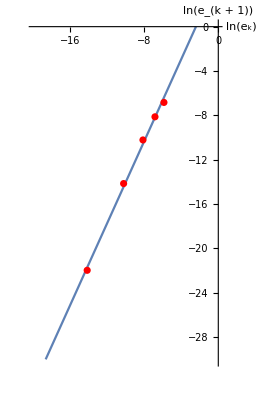

```mathematica
e=Abs[X-1/2 (-4+3 √2)];
ScientificForm[MatrixForm[e],11]
ScientificForm[MatrixForm[Log[e]],11]
Subscript[e, 0]=e[[-6;;-2]];
Subscript[e, 1]=e[[-5;;-1]];
L[x_]=Fit[Transpose[{Log[Subscript[e, 0]],Log[Subscript[e, 1]]}],{1,x},x]
Show[Plot[L[x],{x,-20,0},AxesLabel->{ln["e_k"],ln["e_(k + 1)"]},LabelStyle->Directive[FontFamily->"Century Schoolbook"],PlotRange->{-30,0},AspectRatio->Automatic],ListPlot[Transpose[{Log[Subscript[e, 0]],Log[Subscript[e, 1]]}],PlotStyle->Red]]
```

### 初值为3

```mathematica
Subscript[x, 0] = 3;
X=NestWhileList[N[φ[#]]&,Subscript[x, 0],Abs[f[#]]>=ε&]
Length[X]-1
Show[Plot[Callout[f[x],"f(x)",{1.7,1000},2.4,Background->None,Appearance->"CurvedLeader",LabelStyle->Directive[Italic]],{x,-0.5,3.5},PlotStyle->Directive[RGBColor[0.9,0.5,0.5],Thick],PlotRange->{-200,1500},AxesLabel->{x,y},LabelStyle->Directive[FontFamily->"Century Schoolbook"]],Plot[Evaluate[Table[f'[t](x-t)+f[t],{t,X}]],{x,-0.5,3.5},PlotRange->{-200,1500},PlotStyle->linecolor],ListPlot[Table[Callout[{X[[k]],0},Subscript["x", k-1],Below,LabelStyle->Directive[Italic,FontFamily->"Century Schoolbook"]],{k,1,6}]],
Graphics[{Dashed,Table[Line[{{X[[k]],0},{X[[k]],f[X[[k]]]}}],{k,1,4}]}]]
```

{3,1.91928,1.19361,0.731121,0.453621,0.296637,0.211975,0.167794,0.145194,0.133768,0.128036,0.125196,0.123839,0.123271,0.123119,0.123106,0.123106}

16

-Graphics-

#### 迭代阶估计

(2.8768943744
1.7961694979
1.0705076972
6.0801582897×10^-1
3.3051518047×10^-1
1.735313058×10^-1
8.8869725502×10^-2
4.4688409691×10^-2
2.2088763173×10^-2
1.0661981693×10^-2
4.9308714222×10^-3
2.0904076484×10^-3
7.3309680312×10^-4
1.654033292×10^-4
1.2936988968×10^-5
9.2467084656×10^-8
4.7917225743×10^-12)

(1.0567113701
5.8565634067×10^-1
6.8133019265×10^-2
-4.9755436287×10^-1
-1.1071026889
-1.751397259
-2.42058374
-3.108041102
-3.8126862535
-4.5410709777
-5.3122395475
-6.1703961849
-7.2182328005
-8.7071236474
-1.1255419988×10^1
-1.6196413097×10^1
-2.606413115×10^1)

4.95417+1.90145 x

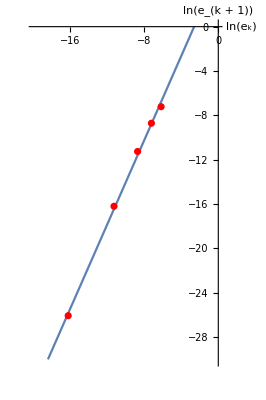

```mathematica
e=Abs[X-(-4+√17)];
ScientificForm[N[MatrixForm[e]],11]
ScientificForm[N[MatrixForm[Log[e]]],11]
Subscript[e, 0]=e[[-6;;-2]];
Subscript[e, 1]=e[[-5;;-1]];
L[x_]=Fit[Transpose[{Log[Subscript[e, 0]],Log[Subscript[e, 1]]}],{1,x},x]
Show[Plot[L[x],{x,-20,0},AxesLabel->{ln["e_k"],ln["e_(k + 1)"]},LabelStyle->Directive[FontFamily->"Century Schoolbook"],PlotRange->{-30,0},AspectRatio->Automatic],ListPlot[Transpose[{Log[Subscript[e, 0]],Log[Subscript[e, 1]]}],PlotStyle->Red]]
```

## 弦截法

```mathematica
φ[{x_,y_}]={y,x-(f[x]*(x-y))/(f[x]-f[y])}
```

{y,x-((1-16 x+61 x^2+24 x^3+2 x^4) (x-y))/(-16 x+61 x^2+24 x^3+2 x^4+16 y-61 y^2-24 y^3-2 y^4)}

### 初值为0, 0.5

```mathematica
Subscript[x, 0] = 0;
Subscript[x, 1]=0.5;
S=NestWhileList[φ,{Subscript[x, 0],Subscript[x, 1]},Abs[f[#[[2]]]]>=ε&];
X=Prepend[S[[All,2]],Subscript[x, 0]]
Length[X]-1
Show[Plot[Callout[f[x],"f(x)",{0.4,3},0.3,Background->None,Appearance->"CurvedLeader",LabelStyle->Directive[Italic]],{x,-0.2,0.6},PlotStyle->Directive[RGBColor[0.9,0.5,0.5],Thick],PlotRange->{-3,13},AxesLabel->{x,y},LabelStyle->Directive[FontFamily->"Century Schoolbook"]],Graphics[Riffle[Table[InfiniteLine[{{S[[k,1]],f[S[[k,1]]]},{S[[k,2]],f[S[[k,2]]]}}],{k,1,5}],linecolor,{1,-2,2}]],ListPlot[Table[Callout[{X[[k]],0},Subscript["x", k-1],Below,LabelStyle->Directive[Italic,FontFamily->"Century Schoolbook"]],{k,1,6}]],
Graphics[{Dashed,Table[Line[{{X[[k]],0},{X[[k]],f[X[[k]]]}}],{k,1,5}]}]]
```

{0,0.5,-0.0481928,-0.158822,0.020529,0.0497041,0.080543,0.0959991,0.106204,0.11229,0.11607,0.118374,0.119772,0.120595,0.121044,0.121248,0.121311,0.12132,0.12132}

18

-Graphics-

#### 迭代阶估计

(1.2132034356×10^-1
3.7867965644×10^-1
1.6951311464×10^-1
2.8014211597×10^-1
1.0079138723×10^-1
7.1616244052×10^-2
4.0777318671×10^-2
2.5321247778×10^-2
1.5116793758×10^-2
9.0301139304×10^-3
5.2506628041×10^-3
2.9461909709×10^-3
1.5478657362×10^-3
7.2558837846×10^-4
2.7651124648×10^-4
7.1931407049×10^-5
9.3156811462×10^-6
3.5877440603×10^-7
1.860823412×10^-9)

(-2.1093207643
-9.7106466498×10^-1
-1.7748249826
-1.2724582475
-2.2947023711
-2.6364333585
-3.1996292671
-3.6761114026
-4.1919489838
-4.7071902948
-5.249400962
-5.8272421392
-6.4708782413
-7.2285276758
-8.1932590634
-9.5397975729
-1.1583811433×10^1
-1.4840572041×10^1
-2.0102246753×10^1)

3.30725+1.57233 x

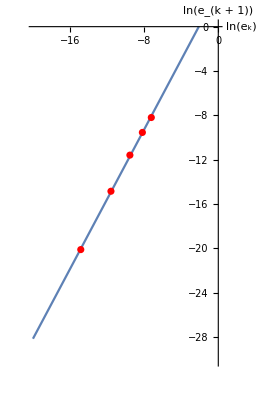

```mathematica
e=Abs[X-1/2 (-4+3 √2)];
ScientificForm[N[MatrixForm[e]],11]
ScientificForm[N[MatrixForm[Log[e]]],11]
Subscript[e, 0]=e[[-6;;-2]];
Subscript[e, 1]=e[[-5;;-1]];
L[x_]=Fit[Transpose[{Log[Subscript[e, 0]],Log[Subscript[e, 1]]}],{1,x},x]
Show[Plot[L[x],{x,-20,0},AxesLabel->{ln["e_k"],ln["e_(k + 1)"]},LabelStyle->Directive[FontFamily->"Century Schoolbook"],PlotRange->{-30,0},AspectRatio->Automatic],ListPlot[Transpose[{Log[Subscript[e, 0]],Log[Subscript[e, 1]]}],PlotStyle->Red]]
```

### 初值为0.1, 1.5

```mathematica
Subscript[x, 0] = 0.1;
Subscript[x, 1]=1.5;
S=NestWhileList[φ,{Subscript[x, 0],Subscript[x, 1]},Abs[f[#[[2]]]]>=ε&];
X=Prepend[S[[All,2]],Subscript[x, 0]]
Length[X]-1
Show[Plot[Callout[f[x],"f(x)",{1.25,70},1.2,Background->None,Appearance->"CurvedLeader",LabelStyle->Directive[Italic]],{x,-0.5,2.0},PlotStyle->Directive[RGBColor[0.9,0.5,0.5],Thick],PlotRange->{-30,220},AxesLabel->{x,y},LabelStyle->Directive[FontFamily->"Century Schoolbook"]],Graphics[Riffle[Table[InfiniteLine[{{S[[k,1]],f[S[[k,1]]]},{S[[k,2]],f[S[[k,2]]]}}],{k,1,5}],linecolor,{1,-2,2}]],ListPlot[Table[Callout[{X[[k]],0},Subscript["x", k-1],Below,LabelStyle->Directive[Italic,FontFamily->"Century Schoolbook"]],{k,1,2}]],
Graphics[{Dashed,Table[Line[{{X[[k]],0},{X[[k]],f[X[[k]]]}}],{k,1,2}]}]]
```

{0.1,1.5,0.0997668,0.0995287,0.110959,0.114687,0.117668,0.119316,0.120338,0.120908,0.121193,0.121298,0.121319,0.12132,0.12132}

14

-Graphics-

```mathematica
Show[Plot[Callout[f[x],"f(x)",{0.110,0.03},0.106,Background->None,Appearance->"CurvedLeader",LabelStyle->Directive[Italic]],{x,0.099,0.122},PlotStyle->Directive[RGBColor[0.9,0.5,0.5],Thick],PlotRange->{-0.02,0.04},AxesLabel->{x,y},LabelStyle->Directive[FontFamily->"Century Schoolbook"]],Graphics[Riffle[Table[InfiniteLine[{{S[[k,1]],f[S[[k,1]]]},{S[[k,2]],f[S[[k,2]]]}}],{k,1,6}],linecolor,{1,-2,2}]],ListPlot[Table[Callout[{X[[k]],0},Subscript["x", k-1],{X[[k]],-0.008},LabelStyle->Directive[Italic,FontFamily->"Century Schoolbook"],Appearance->None],{k,4,9}]],
Graphics[{Dashed,Table[Line[{{X[[k]],0},{X[[k]],f[X[[k]]]}}],{k,4,7}]}]]
```

-Graphics-

#### 迭代阶估计

(2.132034356×10^-2
1.3786796564
2.1553516899×10^-2
2.1791639793×10^-2
1.0361631587×10^-2
6.6329363778×10^-3
3.6525313994×10^-3
2.0043608439×10^-3
9.8274306039×10^-4
4.1241949404×10^-4
1.2734871906×10^-4
2.2574648318×10^-5
1.4846065701×10^-6
1.8511219807×10^-8
1.5369830408×10^-11)

(-3.8480935654
3.2112627048×10^-1
-3.8372162786
-3.8262288785
-4.5696455654
-5.0157076803
-5.6123348177
-6.2124300502
-6.9251628551
-7.7934695372
-8.968581415
-1.0698683037×10^1
-1.3420360757×10^1
-1.7804888813×10^1
-2.4898614592×10^1)

3.58525+1.59693 x

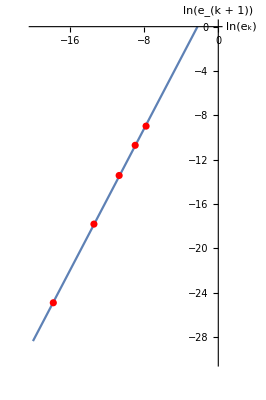

```mathematica
e=Abs[X-1/2 (-4+3 √2)];
ScientificForm[MatrixForm[e],11]
ScientificForm[MatrixForm[Log[e]],11]
Subscript[e, 0]=e[[-6;;-2]];
Subscript[e, 1]=e[[-5;;-1]];
L[x_]=Fit[Transpose[{Log[Subscript[e, 0]],Log[Subscript[e, 1]]}],{1,x},x]
Show[Plot[L[x],{x,-20,0},AxesLabel->{ln["e_k"],ln["e_(k + 1)"]},LabelStyle->Directive[FontFamily->"Century Schoolbook"],PlotRange->{-30,0},AspectRatio->Automatic],ListPlot[Transpose[{Log[Subscript[e, 0]],Log[Subscript[e, 1]]}],PlotStyle->Red]]
```

## 方程的准确值

```mathematica
Solve[f[x]==0,x]
Solve[f'[x]==0,x]
N[f'[1/2 (-4+3 √2)]]
N[f'[-4+√17]]
```

{{x→1/2 (-4-3 √2)},{x→1/2 (-4+3 √2)},{x→-4-√17},{x→-4+√17}}

{{x→Root-6.67Root[-8+61 #1+36 #1^2+4 #1^3&,1]-6.667961777492282},{x→Root-2.45Root[-8+61 #1+36 #1^2+4 #1^3&,2]-2.454251349300146},{x→Root0.122Root[-8+61 #1+36 #1^2+4 #1^3&,3]0.12221312679242737}}

-0.124892

0.124971

```mathematica
φ'[x]
```

((122+144 x+24 x^2) (1-16 x+61 x^2+24 x^3+2 x^4))/((-16+122 x+72 x^2+8 x^3)^2)

```mathematica
ExpandNumerator[((122+144 x+24 x^2) (1-16 x+61 x^2+24 x^3+2 x^4))/((-16+122 x+72 x^2+8 x^3)^2)]
```

(122-1808 x+5162 x^2+11328 x^3+5164 x^4+864 x^5+48 x^6)/((-16+122 x+72 x^2+8 x^3)^2)

```mathematica
ExpandDenominator[(122-1808 x+5162 x^2+11328 x^3+5164 x^4+864 x^5+48 x^6)/((-16+122 x+72 x^2+8 x^3)^2)]
```

(122-1808 x+5162 x^2+11328 x^3+5164 x^4+864 x^5+48 x^6)/(256-3904 x+12580 x^2+17312 x^3+7136 x^4+1152 x^5+64 x^6)

```mathematica
{φ'[0],φ'[3]}
```

{61/128,252560/368449}

```mathematica
N[%]
```

{0.476563,0.685468}

```mathematica
f'[x]
```

-16+122 x+72 x^2+8 x^3

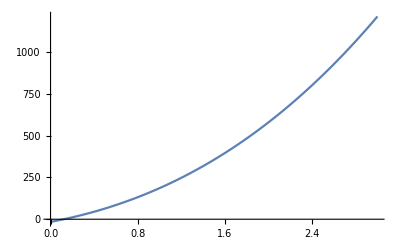

```mathematica
Plot[-16+122 x+72 x^2+8 x^3,{x,0,3}]
```